### Code

```mathematica
Needs["MathOptimizerProGCC`"]
```

Get::noopen: Cannot open MathOptimizerProGCC`.

Needs::nocont: Context MathOptimizerProGCC` was not created when Needs was evaluated.

$Failed

## Geometrical Definitions

### Definitions

```mathematica
regpolypts[n_Integer,d_]:=d/Cos[π/n] Table[AngleVector[θ+π/n-π/2],{θ,0,2(π-1/n),2 π/n}]
```

```mathematica
border[pts_List]:=Line @ Join[pts,{pts⟦1⟧}]
```

### Testing

```mathematica
trianglepts=regpolypts[3, 1];
```

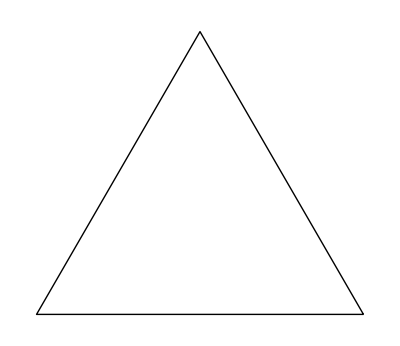

```mathematica
Graphics[border[trianglepts]]
```

## Constraints

### overlapC

#### Definitions

```mathematica
overlapC[radii_List, circlevars_List]:=Table[
(radii⟦i⟧+radii⟦j⟧)^2≤ (circlevars⟦i⟧-circlevars⟦j⟧).(circlevars⟦i⟧-circlevars⟦j⟧),
{i, circlevars//Length}, {j, i+1, circlevars//Length}
]//Flatten
```

#### testing

```mathematica
Clear[r, a, b, c, d, e, f, vars];
```

```mathematica
r={1,1,2};
vars={{a, b}, {c, d}, {e, f}};
```

```mathematica
overlapC[r, vars]
```

{4≤(a-c)^2+(b-d)^2,9≤(a-e)^2+(b-f)^2,9≤(c-e)^2+(d-f)^2}

### Definitions

```mathematica
icons[{{x1_,y1_},{x2_,y2_}},{xc_,yc_},r_]:= r+((y2-y1)*xc+(x1-x2)*yc)/(√((x1-x2)^2+(y1-y2)^2)) ≤ (x1*y2-x2*y1)/(√((x1-x2)^2+(y1-y2)^2))
```

order of points needs to be clockwise

## Optimization Algorithm

```mathematica
cinp[radii_List,polypts_List,obj_,extravwb_List,circlebnd_,opts___]:=
(**)
Block[
{ncircs = Length[radii],npts = Length[polypts],circvars,x,y,circbnds, circvwb,vwb,cons1,brdr,cons2,cons,res},
circvars = Flatten @ Table[{x[i],y[i]},{i,ncircs}];
circbnds = Table[circlebnd,{2*ncircs}];
circvwb = Transpose[{circvars,-circbnds,circbnds}];
vwb = Join[circvwb,extravwb];
cons1=Flatten [Table[(radii⟦i⟧+radii⟦j⟧)^2 ≤  (x[i]-x[j])^2+(y[i]-y[j])^2,{i,ncircs-1},{j,i+1,ncircs}]];
brdr = Partition[Join[polypts,{polypts⟦1⟧}],2,1];
cons2 = Flatten @ Table[icons[brdr⟦j⟧,{x[i],y[i]},radii⟦i⟧],{i,ncircs},{j,npts}];
cons = Join[cons1,cons2];
res = NMinimize[{obj,cons},vwb,opts];
Print[res⟦{1,3}⟧];
res⟦2⟧
]
```

```mathematica
plt[sln_List,radii_List,polypts_List]:=Block[{n = Length[radii]},
Show[Graphics @ border[polypts]/.sln, 
Graphics @ Table[{Hue[i/n],Disk[{x[i],y[i]},radii⟦i⟧]},{i,Length[radii]}]/.sln, ImageSize -> Small]]
```

## Tests

#### equilateral triangle

```mathematica
epts = regpolypts[3,d]
```

{{√3 d,-d},{0,2 d},{-√3 d,-d}}

```mathematica
AbsoluteTiming[test1 = cinp[Range[10]^(-1/2),epts,d,{{d,0,2}},2]]
```

{1.56432,Maximum Constraint Violation→4.44089×10^-16}

{1.29045,{x[1]→0.,y[1]→1.12864,x[2]→-1.48473,y[2]→-0.857212,x[3]→1.12586,y[3]→0.0238883,x[4]→1.79286,y[4]→-0.979791,x[5]→-1.14747,y[5]→0.246738,x[6]→0.898267,y[6]→-1.15607,x[7]→0.112637,y[7]→-1.18635,x[8]→0.171203,y[8]→-0.457185,x[9]→-0.449746,y[9]→-0.750843,x[10]→-0.468097,y[10]→-0.101542,d→1.56432}}

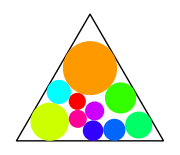

```mathematica
p1=plt[test1,Range[10]^(-1/2),epts]
```

#### right triangle with equal sides

```mathematica
rpts = {{0,0},{d,0},{0,d}};
```

```mathematica
test2 = cinp[Range[10]^(-1/2),rpts,d,{{d,0,5}},6]
```

{4.99749,Maximum Constraint Violation→2.22045×10^-15}

{x[1]→1.,y[1]→1.,x[2]→3.29038,y[2]→0.707107,x[3]→2.43159,y[3]→1.66226,x[4]→1.26168,y[4]→2.58864,x[5]→0.447214,y[5]→3.91782,x[6]→0.408248,y[6]→2.27789,x[7]→2.2464,y[7]→0.411244,x[8]→1.07578,y[8]→3.4217,x[9]→0.450551,y[9]→3.13728,x[10]→2.0706,y[10]→2.47967,d→4.99749}

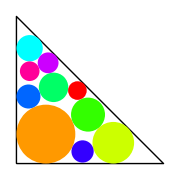

```mathematica
p2=plt[test2,Range[10]^(-1/2),rpts]
```

#### right triangle with unequal sides

```mathematica
rptsu = {{0,0},{w,0},{0,h}};
```

```mathematica
test3 = cinp[Range[10]^(-1/2),rptsu,√(w*h),{{w,0,6},{h,0,6}},6]
```

{4.92116,Maximum Constraint Violation→2.61746×10^-9}

{x[1]→2.3889,y[1]→1.,x[2]→0.707107,y[2]→0.707107,x[3]→1.70459,y[3]→2.42118,x[4]→0.5,y[4]→3.82419,x[5]→3.72638,y[5]→0.447214,x[6]→0.720077,y[6]→2.37494,x[7]→1.08869,y[7]→3.15237,x[8]→0.353553,y[8]→1.70711,x[9]→0.333333,y[9]→3.00769,x[10]→1.24659,y[10]→1.6539,w→4.75603,h→5.09202}

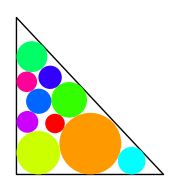

```mathematica
p3=plt[test3,Range[10]^(-1/2),rptsu]
```

#### rectangle

```mathematica
rectpts = {{w,h},{-w,h},{-w,-h},{w,-h}};
```

```mathematica
test4 = cinp[Range[10]^(-1/2),rectpts,√(w*h),{{w,0,2},{h,0,2}},2]
```

{1.73521,Maximum Constraint Violation→2.57481×10^-9}

{x[1]→-0.776941,y[1]→0.69445,x[2]→-1.06983,y[2]→-0.987343,x[3]→0.566225,y[3]→-1.1171,x[4]→1.27694,y[4]→0.3826,x[5]→0.448146,y[5]→-0.0759977,x[6]→1.36869,y[6]→1.2862,x[7]→0.588677,y[7]→0.927681,x[8]→1.42339,y[8]→-0.674527,x[9]→1.44361,y[9]→-1.36112,x[10]→-0.137233,y[10]→-0.566074,w→1.77694,h→1.69445}

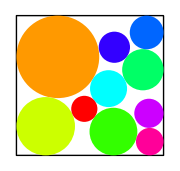

```mathematica
p4=plt[test4,Range[10]^(-1/2),rectpts]
```

#### hexagon

```mathematica
hex = regpolypts[6,d]
```

{{d/(√3),-d},{(2 d)/(√3),0},{d/(√3),d},{-d/(√3),d},{-(2 d)/(√3),0},{-d/(√3),-d}}

```mathematica
test5 = cinp[Range[10]^(-1/2),hex,d,{{d,0,2}},2]
```

{1.85683,Maximum Constraint Violation→5.9489×10^-9}

{x[1]→-0.494692,y[1]→-0.856831,x[2]→1.13194,y[2]→-0.338871,x[3]→-1.14152,y[3]→0.581797,x[4]→0.34936,y[4]→0.580191,x[5]→0.806815,y[5]→1.40962,x[6]→0.853474,y[6]→-1.41891,x[7]→1.28292,y[7]→0.735644,x[8]→-0.876621,y[8]→1.47569,x[9]→-0.35035,y[9]→1.0328,x[10]→0.0546947,y[10]→1.5406,d→1.85683}

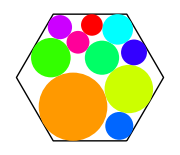

```mathematica
p5=plt[test5,Range[10]^(-1/2),hex]
```

#### stretched hexagon

```mathematica
shex = regpolypts[6,1]/. {x_,y_} -> {w*x,h*y}
```

{{w/(√3),-h},{(2 w)/(√3),0},{w/(√3),h},{-w/(√3),h},{-(2 w)/(√3),0},{-w/(√3),-h}}

```mathematica
test6 = cinp[Range[10]^(-1/2),shex,√(w*h),{{w,0,2},{h,0,2}},2]
```

{1.88331,Maximum Constraint Violation→4.90608×10^-12}

{x[1]→-0.459707,y[1]→0.915032,x[2]→-0.88057,y[2]→-0.739382,x[3]→1.23607,y[3]→-0.335261,x[4]→1.1159,y[4]→0.735366,x[5]→0.884135,y[5]→-1.29749,x[6]→0.781711,y[6]→1.5799,x[7]→0.285093,y[7]→-0.244303,x[8]→0.155961,y[8]→-0.964334,x[9]→0.190182,y[9]→-1.65481,x[10]→-0.459154,y[10]→-1.67192,w→1.784,h→1.98815}

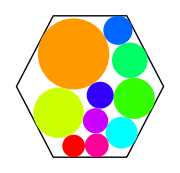

```mathematica
p6=plt[test6,Range[10]^(-1/2),shex]
```

```mathematica
all ={p1,p2,p3,p4,p5,p6}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Scratch

```mathematica
s={{1,1}, {1,2}}
```

{{1,1},{1,2}}

```mathematica
s⟦1⟧.s⟦2⟧
```

3

```mathematica
{1,1}.{1,2}
```

3

```mathematica
(y2-y1)*xc+(x1-x2)*yc-(x1*y2-x2*y1)
```

x2 y1-x1 y2+xc (-y1+y2)+(x1-x2) yc

```mathematica
-%//Expand
```

-x2 y1+xc y1+x1 y2-xc y2-x1 yc+x2 yc